{{S→InterpolatingFunction[…],M→InterpolatingFunction[…]}}

{{0,10.0124},{5,10.2552},{7,10.3378},{9,10.4132},{12,10.5141},{14,10.574},{16,10.6286},{19,10.7016},{21,10.7449},{23,10.7845},{26,10.8373},{28,10.8687},{30,10.8974},{33,10.9357}}

{{0,10.0124},{5,10.2017},{7,10.5397},{9,10.4451},{12,10.4856},{14,10.702},{16,10.702},{19,10.8642},{21,10.8237},{23,10.9859},{26,11.1346},{28,11.1617},{30,11.3239},{33,11.2563}}

{0.920455,0.613636,0.715909,0.613636,0.647727,0.715909,0.75,0.681818,0.613636,0.545455,0.511364,0.511364,0.545455,0.715909}

{{0,10.0124,0.920455},{5,10.2017,0.613636},{7,10.5397,0.715909},{9,10.4451,0.613636},{12,10.4856,0.647727},{14,10.702,0.715909},{16,10.702,0.75},{19,10.8642,0.681818},{21,10.8237,0.613636},{23,10.9859,0.545455},{26,11.1346,0.511364},{28,11.1617,0.511364},{30,11.3239,0.545455},{33,11.2563,0.715909}}

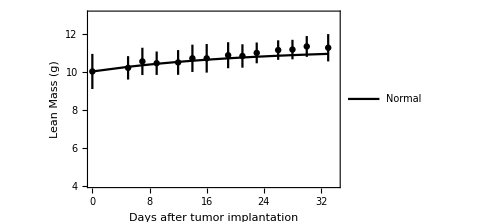

```mathematica
P0=0.479; P1=0.133; v0=0.087; v1=5.591; m=1000 ; d=0.05; (*The parameters are fitted with experimental data for mouse model, based on RMSE minimum method my other code*)
(*Simple NDSolve to find stem and Muscle cell population*)
s=NDSolve[{S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m))* S[x]-d*M[x],S[0]==250.31,M[0]==4755.9},{S,M},{x,0,500}]
jm1=(0.002*M[0]/.s)[[1]]; jm2=(0.002*M[5]/.s)[[1]] ; jm3=(0.002*M[7]/.s)[[1]]; jm4=(0.002*M[9]/.s)[[1]]; jm5=(0.002*M[12]/.s)[[1]]; jm6=(0.002*M[14]/.s)[[1]]; jm7=(0.002*M[16]/.s)[[1]]; jm8=(0.002*M[19]/.s)[[1]]; jm9=(0.002*M[21]/.s)[[1]]; jm10=(0.002*M[23]/.s)[[1]]; jm11=(0.002*M[26]/.s)[[1]]; jm12=(0.002*M[28]/.s)[[1]];
jm13=(0.002*M[30]/.s)[[1]]; jm14=(0.002*M[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
js1=(0.002*S[0]/.s)[[1]]; js2=(0.002*S[5]/.s)[[1]]; js3=(0.002*S[7]/.s)[[1]]; js4=(0.002*S[9]/.s)[[1]]; js5=(0.002*S[12]/.s)[[1]]; js6=(0.002*S[14]/.s)[[1]];js7=(0.002*S[16]/.s)[[1]]; js8=(0.002*S[19]/.s)[[1]]; js9=(0.002*S[21]/.s)[[1]]; js10=(0.002*S[23]/.s)[[1]]; js11=(0.002*S[26]/.s)[[1]]; js12=(0.002*S[28]/.s)[[1]];
js13=(0.002*S[30]/.s)[[1]];  js14=(0.002*S[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
j1=jm1+js1; j2=jm2+js2; j3=jm3+js3; j4=jm4+js4; j5=jm5+js5; j6=jm6+js6; j7=jm7+js7; j8=jm8+js8; j9=jm9+js9; j10=jm10+js10; j11=jm11+js11; j12=jm12+js12;
j13=jm13+js13; j14=jm14+js14;
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
data1=List[{0,j1},{5,j2},{7,j3},{9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9},{23,j10},{26,j11},{28,j12},{30,j13},{33,j14}]
data2=Import["D:/LBMblack1.txt",{"Data",{All},{1,2}}]
error=Import["D:/Errorbar0.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error}]
Needs["ErrorBarPlots`"]
G1=ListLinePlot[Split[data1,#2=!={0,0}&](*,PlotMarkers->Automatic*),AxesLabel->{"Time (days)","Lean Mass(g)"},AxesStyle->Directive[Black,12],PlotLegends->Placed[{"Normal"},{0.15,0.3}],PlotStyle->Black,PlotRange->{{-0.001,34},{4.1,13}}];
pl1=Show[G1,ErrorListPlot[withError,PlotStyle->Black,(*PlotLegends->{"Normal, Experimental data"},*)ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{"Days after tumor implantation","Lean Mass (g)"},FrameStyle->Directive[Black,12]]
```

{{0,10.0992},{5,9.83952},{7,9.59825},{9,9.3092},{12,8.81812},{14,8.46898},{16,8.11267},{19,7.57899},{21,7.23102},{23,6.89371},{26,6.41379},{28,6.11426},{30,5.83287},{33,5.44728}}

{{0,10.0991},{5,10.3081},{7,10.353},{9,10.3363},{12,9.95988},{14,9.73706},{16,9.2575},{19,7.67494},{21,7.34486},{23,6.8773},{26,6.16878},{28,5.73076},{30,5.62033},{33,4.76201}}

{0.369748,0.605042,0.605042,0.638655,0.974929,1.21022,1.14286,1.0084,0.672269,0.571429,0.571568,0.87381,0.604903,0.638655}

{{0,10.0991,0.369748},{5,10.3081,0.605042},{7,10.353,0.605042},{9,10.3363,0.638655},{12,9.95988,0.974929},{14,9.73706,1.21022},{16,9.2575,1.14286},{19,7.67494,1.0084},{21,7.34486,0.672269},{23,6.8773,0.571429},{26,6.16878,0.571568},{28,5.73076,0.87381},{30,5.62033,0.604903},{33,4.76201,0.638655}}

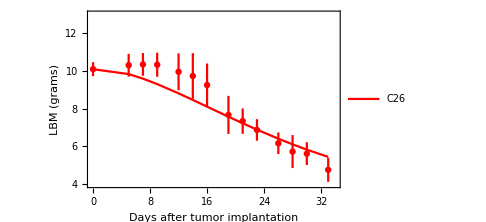

```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.49941;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;d2=0.0; (*Fitted parameters with c26-tumore bearing mice*)
s=NDSolve[{T'[x]==(0.244597*T[x])/((1+(T[x]/1088.66)^μ)^(1/μ)),S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))* S[x]-(d+((d2*T[x])/(1+(T[x]/m2))))*M[x],T[0]==6.86,S[0]==252.5,M[0]==4797.08},{T,S,M},{x,0,100}];

jm1=(0.002*M[0]/.s)[[1]]; jm2=(0.002*M[5]/.s)[[1]]; jm3=(0.002*M[7]/.s)[[1]]; jm4=(0.002*M[9]/.s)[[1]]; jm5=(0.002*M[12]/.s)[[1]]; jm6=(0.002*M[14]/.s)[[1]];jm7=(0.002*M[16]/.s)[[1]]; jm8=(0.002*M[19]/.s)[[1]]; jm9=(0.002*M[21]/.s)[[1]]; jm10=(0.002*M[23]/.s)[[1]]; jm11=(0.002*M[26]/.s)[[1]]; jm12=(0.002*M[28]/.s)[[1]];
jm13=(0.002*M[30]/.s)[[1]]; jm14=(0.002*M[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
js1=(0.002*S[0]/.s)[[1]]; js2=(0.002*S[5]/.s)[[1]]; js3=(0.002*S[7]/.s)[[1]]; js4=(0.002*S[9]/.s)[[1]]; js5=(0.002*S[12]/.s)[[1]]; js6=(0.002*S[14]/.s)[[1]];js7=(0.002*S[16]/.s)[[1]]; js8=(0.002*S[19]/.s)[[1]]; js9=(0.002*S[21]/.s)[[1]]; js10=(0.002*S[23]/.s)[[1]]; js11=(0.002*S[26]/.s)[[1]]; js12=(0.002*S[28]/.s)[[1]];
js13=(0.002*S[30]/.s)[[1]]; js14=(0.002*S[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
jt1=(0.002*T[0]/.s)[[1]]; jt2=(0.002*T[5]/.s)[[1]]; jt3=(0.002*T[7]/.s)[[1]]; jt4=(0.002*T[9]/.s)[[1]]; jt5=(0.002*T[12]/.s)[[1]]; jt6=(0.002*T[14]/.s)[[1]];jt7=(0.002*T[16]/.s)[[1]]; jt8=(0.002*T[19]/.s)[[1]]; jt9=(0.002*T[21]/.s)[[1]]; jt10=(0.002*T[23]/.s)[[1]]; jt11=(0.002*T[26]/.s)[[1]];jt12=(0.002*T[28]/.s)[[1]]; jt13=(0.002*T[30]/.s)[[1]]; jt14=(0.002*T[33]/.s)[[1]];
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
j1=jm1+js1; j2=jm2+js2; j3=jm3+js3; j4=jm4+js4; j5=jm5+js5; j6=jm6+js6; j7=jm7+js7; j8=jm8+js8; j9=jm9+js9; j10=jm10+js10; j11=jm11+js11;
j12=jm12+js12; j13=jm13+js13; j14=jm14+js14;
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
data1=List[{0,j1},{5,j2},{7,j3},{9,j4},{12,j5},{14,j6},{16,j7},{19,j8},{21,j9},{23,j10},{26,j11},{28,j12}, {30,j13}, {33,j14} ]
data2=Import["D:/LBM.txt",{"Data",{All},{1,2}}]
error=Import["D:/Errorbar.txt",{"Data",{All},{1}}]
withError=Transpose[{data2[[All,1]],data2[[All,2]],error}]
Needs["ErrorBarPlots`"]
G1=ListLinePlot[Split[data1,#2=!={0,0}&],PlotStyle->Red,(*PlotMarkers->Automatic,*)AxesStyle->Directive[Black,12],PlotLegends->Placed[{"C26"},{0.12,0.2}],PlotRange->{{-0.1,34},{4,13}}];
pl2=Show[G1,ErrorListPlot[withError,PlotStyle->Red(*,PlotLegends->{"Experimental data"}*),ImageSize->Medium,Frame->True],ImageSize->Medium,Frame->True,FrameLabel->{"Days after tumor implantation","LBM (grams)"},FrameStyle->Directive[Black,12]]
```

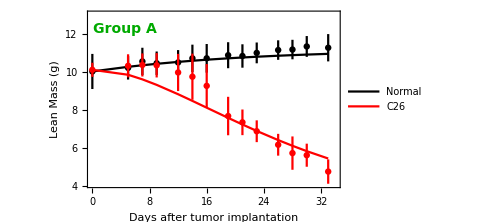

```mathematica
ppl1=Show[pl1,pl2,Epilog->Text[Style["Group A",Darker[Green],Bold,Italic,14],Scaled[{.15,.9}]]]
```

```mathematica
Export["D:/All1.eps",ppl1]
```

D:/All1.eps